## RNN Sequence 96 Rescaled

```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"];
```

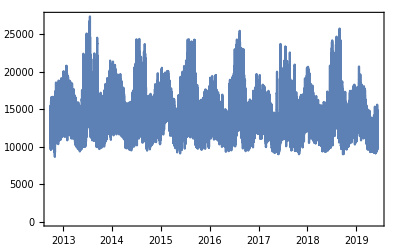

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=loadTimeSeriesResampled//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,96,1];valuesp = values[[97;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,96}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

```mathematica
58680
```

58680

```mathematica
Length@threaddata
```

58640

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",96}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

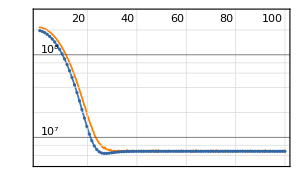
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:7.2min  examples/s:10579
data | ,,  training examples:45000  validation examples:13584  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.8×10^6
validation | ,,  loss:6.76×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet=NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→313500.|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{15571.1,15650.6,15550.,15302.7,15084.7,15006.5,15040.4,15374.6,15861.4,16102.7,16253.8,15728.2,14725.2,13468.8,12628.2,12192.5,11892.3,11734.9,11756.3,11787.6,12538.3,14211.6,15276.5,15579.4,15528.3,15204.2,14817.9,14651.6,14463.1,14221.3,14125.9,14382.,14516.6,14935.4,15450.,15188.9,14329.5,13169.8,12186.3,12101.6,12083.4,12240.9,12305.6,12419.8,13003.6,14180.,14862.8,14680.7,14187.2,13634.8,13336.7,13077.,12740.2,12956.9,13126.7,13239.6,13700.3,14094.1,14587.8,14369.5,13755.3,12871.4,11648.4,11485.9,11075.5,10877.7,10828.,10951.7,11162.2,11860.3,12570.9,13046.8,12917.2,12480.5,12111.6,12008.9,12131.9,12110.4,11984.3,12376.6,12874.8,13339.7,13854.,13696.2,13187.8,12453.8,11907.6,11114.4,10910.2,10951.7,10883.2,10954.5,11021.,11385.1,11920.2,12696.2}}→13192.6,{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4,14470.4,13671.2,12882.6,11482.3,11488.6,11321.4,11271.6,11207.5,11164.,11698.8,12995.8,13763.7,13754.4,13510.9,13247.,12939.6,12614.5,12884.1,12956.,12960.6,12932.,13266.2,13733.8,14164.,14198.8,13421.4,12296.2,11899.4,10705.8,10468.1,10380.3,10531.2,10627.1,11465.3,12671.2,13836.5,14392.9,14611.7,14683.5,14466.1,14217.6,14286.4,14257.4,13977.2,13828.2,13922.9,14254.5,14587.8,14546.2,13792.7,12674.6,11331.6,10999.9,10580.5,10686.1,10691.,11017.1,11662.3,12920.1,13594.5,13446.1,13095.9,12998.,12600.5,12621.1,12295.,12006.9,12111.5,12547.2,12790.,13161.7,13563.6,13729.1,13157.1,12272.8,10844.2}}→10644.8}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:7.2min  examples/s:10579
data | ,,  training examples:45000  validation examples:13584  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.8×10^6
validation | ,,  loss:6.76×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4,14470.4,13671.2,12882.6,11482.3,11488.6,11321.4,11271.6,11207.5,11164.,11698.8,12995.8,13763.7,13754.4,13510.9,13247.,12939.6,12614.5,12884.1,12956.,12960.6,12932.,13266.2,13733.8,14164.,14198.8,13421.4,12296.2,11899.4,10705.8,10468.1,10380.3,10531.2,10627.1,11465.3,12671.2,13836.5,14392.9,14611.7,14683.5,14466.1,14217.6,14286.4,14257.4,13977.2,13828.2,13922.9,14254.5,14587.8,14546.2,13792.7,12674.6,11331.6,10999.9,10580.5,10686.1,10691.,11017.1,11662.3,12920.1,13594.5,13446.1,13095.9,12998.,12600.5,12621.1,12295.,12006.9,12111.5,12547.2,12790.,13161.7,13563.6,13729.1,13157.1,12272.8,10844.2}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
tvalues=Table[trainednet[testdata[[i,1]]],{i,1,Length@testdata}]
```

$Aborted[]

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100]
```

{10953.7,195}
 |  |  |  |

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```

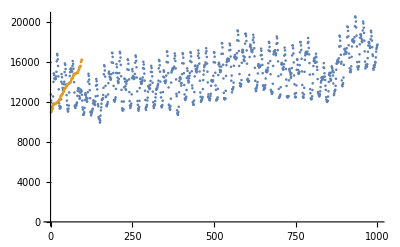

-Graphics-